```mathematica
Manipulate[SetOptions[EvaluationNotebook[],WindowOpacity->x];x,{{x,0.8},0.5,1}]
```

# 沃罗内网格（笔记本）

产生点阵可以直接用基底来产生，比如：

```mathematica
b={{-√3,-1},{-√3,1}}
```

{{-√3,-1},{-√3,1}}

产生点阵：

```mathematica
p=Tuples[Range[0,4],2].b
```

{{0,0},{-√3,1},{-2 √3,2},{-3 √3,3},{-4 √3,4},{-√3,-1},{-2 √3,0},{-3 √3,1},{-4 √3,2},{-5 √3,3},{-2 √3,-2},{-3 √3,-1},{-4 √3,0},{-5 √3,1},{-6 √3,2},{-3 √3,-3},{-4 √3,-2},{-5 √3,-1},{-6 √3,0},{-7 √3,1},{-4 √3,-4},{-5 √3,-3},{-6 √3,-2},{-7 √3,-1},{-8 √3,0}}

画图看看：

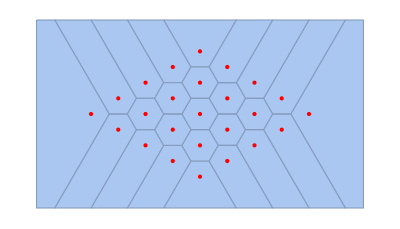

```mathematica
Show[VoronoiMesh[p],Epilog->{Red,Point[p]}]
```

这样的话，当我们需要在一个矩形内产生某个缩放比例为μ的点阵，只需要以它的中心为原点，产生一个足够大的点阵，把点阵跟矩形的交集找出来就行。
写一个产生矩形内指定比例点阵的函数：

```mathematica
Generate[Rectangle[{xmin_,ymin_},{xmax_,ymax_}],μ_]:=Module[{n,a,p,pp,b={{-√3,-1},{-√3,1}}},a={(xmin+xmax)/2,(ymin+ymax)/2};n=Ceiling[Sqrt[(xmin-xmax)^2+(ymin-ymax)^2]*Sqrt[2]*3/(2μ)];
p=Point[(a+#)&/@Tuples[Table[i,{i,-n,n}],2].(μ b)];
pp=RegionIntersection[p,Rectangle[{xmin,ymin},{xmax,ymax}]];
Return[pp]]
```

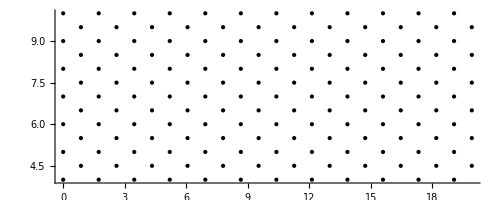

```mathematica
Graphics[Generate[Rectangle[{0.,4},{20,10}],0.5],Axes->True]
```

接下来编写一个函数来产生5个矩形区域。为了产生着5个区域，其实只需要输入四个值就行。分别是大矩形左下角点，右上角点；以及中间矩形左下，右上。

```mathematica
Rectanglela[{x1min_,y1min_},{x1max_,y1max_},{x2min_,y2min_},{x2max_,y2max_}]:={Rectangle[{x2min,y2min},{x2max,y2max}],Rectangle[{x1min,y1min},{x2min,y1max}],Rectangle[{x2min,y2max},{x2max,y1max}],Rectangle[{x2max,y1min},{x1max,y1max}],Rectangle[{x2min,y1min},{x2max,y2min}]}
```

以上代码形成这样的布局：

-Graphics-

产生的效果如下：

```mathematica
j=Rectanglela[{0,0},{20,20},{6,6},{14,14}]
```

{Rectangle[{6,6},{14,14}],Rectangle[{0,0},{6,20}],Rectangle[{6,14},{14,20}],Rectangle[{14,0},{20,20}],Rectangle[{6,0},{14,6}]}

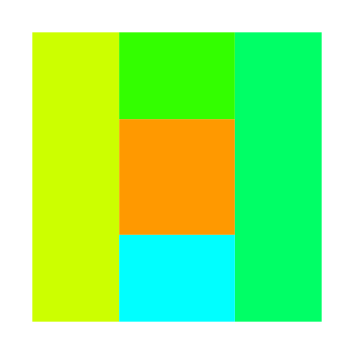

```mathematica
Graphics[Table[{Hue[i/10],j[[i]]},{i,1,5}]]
```

接下来我们就可以设定不同的比率来产生点阵。

```mathematica
a=Thread[Generate[j,{0.1,0.2,0.3,0.4,0.5}]];
```

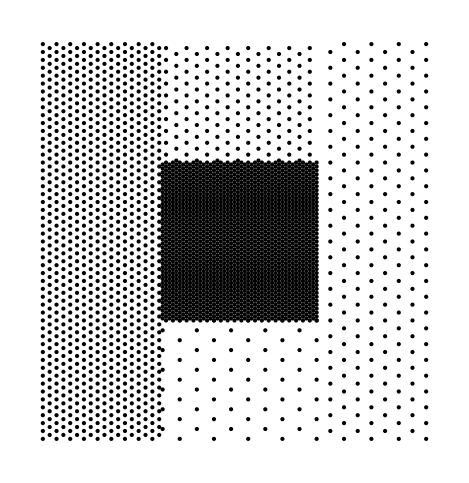

```mathematica
Graphics[a]
```

以上得到的是以Point为头部的表达式，为了将它化为列表，我们采取如下步骤：

```mathematica
Partition[Map[Apply[List,#]&,a]//Flatten,2]//Point
```

Point[{{13.8564,14.},{13.8564,13.8},{13.6832,13.9},{13.51,14.},{13.8564,13.6},{13.6832,13.7},{13.51,13.8},{13.3368,13.9},{13.1636,14.},{13.8564,13.4},{13.6832,13.5},{13.51,13.6},3168,{9.52628,0.5},{8.66025,1.},{7.79423,1.5},{6.9282,2.},{6.06218,2.5},{8.66025,0.},{7.79423,0.5},{6.9282,1.},{6.06218,1.5},{6.9282,0.},{6.06218,0.5}}]
 |  |  |  |

然后想要畸变的话就采取原来我们已经编写好的那个畸变函数就行。